## GeneticAlgorithm on a binary tree with custom crossover and mutation functions

```mathematica
ClearAll[tree, num, res]
AddNumber[tree_Graph, num_]:= 
Module[{},
	If[
		Length[VertexList[tree]] == 0,
		res = VertexAdd[tree, num],
		root = First[Select[VertexList[tree], VertexInDegree[tree, #] == 0 &]];
		If[Length[EdgeList[tree]] == 0,
           source = root,
           source =  
			NestWhile[
				With[
					{node = #},
					neighbors = Select[EdgeList[tree], #[[1]] == node &];
					If[
						num < node,
						First[Select[neighbors, #[[2]] < node &]][[2]],
						First[Select[neighbors, #[[2]] ≥ node &]][[2]]
					]
				]&,
				root,
				With[
					{node = #},
					neighbors = Select[EdgeList[tree], #[[1]] == node &];
					If[
						num < node,
						Length[Select[neighbors, #[[2]] < node &]] > 0,
						Length[Select[neighbors, #[[2]] ≥ node &]] > 0
					]
				]&
			];
		];
		res = EdgeAdd[tree, DirectedEdge[source, num]];
	];
	res
]
```

```mathematica
CreateTree[l_List] := 
	Module[{i},
		g2 = Graph[{}];
		For[i = 1, i ≤ Length[l], ++i, g2 = AddNumber[g2, l[[i]]]];
		g2
	]
```

```mathematica
PermutationMutation[perm_] := 
	Module[{element1, element2},
		element1 = RandomChoice[perm];
		element2 = RandomChoice[perm];
		pe = perm /. element1 -> a;
		pe = pe /. element2 -> element1;
		pe = pe /. a ->  element2;
		pe
	]
```

```mathematica
PermutationCrossover[perm1_, perm2_] :=
	Module[{rule1, rule2},
		rule1 = FindPermutation[perm1];
		rule2 = FindPermutation[perm2];
		Permute[Permute[Range[Length[perm1]], perm1], rule2]
	]
```

```mathematica
PermutationFitness[perm_] := 
	Module[{},
		gra = CreateTree[perm];
		root = First[Select[VertexList[gra], VertexInDegree[gra, #] == 0 &]];
		1/Variance[Join[{N[Log[2, Length[perm]]]}, Length[First[FindPath[gra, root, #]]]& /@ Select[VertexList[gra], VertexOutDegree[gra, #] == 0 &]]]
	]
```

```mathematica
ClearAll[f, init, c];
init = Permute[Range[20], RandomPermutation[20]];
c[x_] := True;

result = GeneticAlgorithm[init, PermutationFitness, {c}, PermutationCrossover, PermutationMutation];
Graph[CreateTree[#], VertexLabels->"Name"]& /@ First[First[result]] // Row
Graph[CreateTree[#], VertexLabels->"Name"]& /@ Last[Last[result]] // Row
Mean[PermutationFitness[#]& /@ First[First[result]]]
Mean[PermutationFitness[#]& /@ Last[Last[result]]]
```

population={{12,14,20,3,16,18,19,5,9,10,6,11,2,1,15,13,4,8,7,17},{12,11,20,3,16,18,19,5,9,10,6,14,2,1,15,13,4,8,7,17},{12,11,20,3,16,18,19,7,9,10,6,14,2,1,15,13,4,8,5,17},{12,2,20,3,16,18,19,5,9,10,6,14,11,1,15,13,4,8,7,17},{12,14,20,3,16,18,19,5,9,10,6,11,2,15,1,13,4,8,7,17}}

population={{12,2,20,3,16,18,19,5,9,10,6,14,11,1,15,4,13,8,7,17},{12,2,20,3,16,18,19,5,9,10,6,14,11,1,15,13,4,8,7,17},{12,14,20,3,16,18,19,5,9,10,6,11,2,1,15,13,4,8,7,17},{12,11,20,3,16,18,19,7,1,10,6,14,2,9,15,13,4,8,5,17},{12,11,20,3,16,18,19,7,9,10,6,14,2,1,15,13,4,8,5,17}}

population={{12,11,20,3,16,18,13,7,1,10,6,14,2,9,15,19,4,8,5,17},{12,11,20,3,16,18,19,8,9,10,6,14,2,1,15,13,4,7,5,17},{12,11,20,3,16,18,19,7,9,10,6,14,2,1,15,13,4,8,5,17},{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,11,20,3,16,18,19,7,9,10,6,14,2,1,15,13,4,8,5,17}}

population={{12,11,10,3,16,18,19,7,9,20,6,14,2,1,15,13,4,8,5,17},{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,6,20,3,16,11,19,5,9,10,14,18,2,1,15,13,4,8,7,17},{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,6,20,3,16,15,19,5,9,10,14,11,2,1,18,13,4,8,7,17}}

population={{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,6,20,3,16,15,19,5,9,10,14,11,2,1,18,13,4,8,7,17},{12,6,20,3,16,15,19,5,9,10,14,11,2,1,18,13,4,8,7,17},{12,6,15,3,16,18,19,5,9,10,14,11,2,1,20,13,4,8,7,17}}

population={{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{16,6,20,3,12,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,6,15,3,16,18,19,5,9,10,20,11,2,1,14,13,4,8,7,17},{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17}}

population={{12,19,20,3,16,18,6,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,16,15,3,6,18,19,5,9,10,20,11,2,1,14,13,4,8,7,17},{12,6,20,3,16,18,19,5,9,10,14,11,2,1,15,13,4,8,7,17},{12,6,15,3,16,18,19,5,9,10,20,11,2,1,14,13,4,8,7,17},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,10,18,19,5,9,16,14,11,2,1,15,13,4,8,7,17},{14,6,20,3,16,18,19,5,9,10,12,11,17,1,15,13,4,8,7,2},{12,19,20,3,16,18,6,5,9,10,14,11,2,1,15,13,4,8,7,17}}

population={{10,6,20,3,16,18,19,5,9,12,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,13,11,17,1,15,14,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{4,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,12,8,7,2}}

population={{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,2,19,5,9,10,14,11,17,1,15,13,4,8,7,18},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,15,18,19,5,9,10,14,11,17,1,16,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,15,18,19,5,9,10,14,11,17,1,16,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,15,11,17,1,14,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,9,18,19,5,16,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,16,3,20,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,13,19,5,9,10,14,11,17,1,15,18,4,8,7,2},{12,6,20,3,16,18,17,5,9,10,14,11,19,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,1,9,10,14,11,17,5,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,17,5,2,10,14,11,19,1,15,13,4,8,7,9},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,16,3,20,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,7,11,17,1,15,13,4,8,14,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,2,14,11,17,1,15,13,4,8,7,10},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,8,5,9,10,14,11,17,1,15,13,4,19,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,5,9,2,4,11,17,1,15,13,14,8,7,10},{12,6,20,3,16,18,8,5,9,10,14,11,17,1,15,13,4,19,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,8,13,4,15,7,2},{12,6,20,3,16,18,19,5,9,2,14,11,17,1,15,13,4,8,7,10}}

population={{12,6,20,3,16,18,19,5,9,2,14,11,17,1,15,13,4,8,7,10},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,8,13,4,15,7,2},{12,18,20,3,16,6,19,5,9,2,14,11,17,1,15,13,4,8,7,10}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,8,13,4,15,7,2},{12,6,20,3,16,18,19,9,15,10,14,11,17,1,8,13,4,5,7,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,7,1,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,7,1,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,2,4,8,7,13},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,7,1,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,7,1,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,7,1,15,13,4,8,17,2}}

population={{12,6,20,3,9,18,19,16,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,19,16,18,3,9,5,10,14,11,17,1,15,2,4,8,7,13},{12,6,20,3,16,18,19,9,5,10,14,11,7,1,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,9,19,5,10,14,11,7,1,15,13,4,8,17,2}}

population={{12,6,20,3,4,18,9,19,5,10,14,11,7,1,15,13,16,8,17,2},{12,6,20,3,16,18,19,1,5,10,14,11,7,9,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,13,1,15,17,4,8,7,2},{12,6,20,3,16,18,9,19,5,10,14,11,7,1,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,9,19,5,10,14,11,7,1,15,13,4,8,17,2},{12,18,20,3,16,6,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,9,19,5,10,14,15,7,1,11,13,4,8,17,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,9,19,5,10,14,11,7,1,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,4,20,3,16,18,19,9,5,10,14,11,17,1,15,13,6,8,7,2},{12,6,20,3,14,18,19,9,5,10,16,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,9,19,5,10,14,11,7,1,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{1,6,20,3,16,18,9,19,5,10,14,11,7,12,15,13,4,8,17,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,15,17,1,11,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,7,10,14,11,17,1,15,13,4,8,5,2},{12,6,20,3,17,18,9,19,5,10,14,11,7,1,15,13,4,8,16,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,2,4,8,7,13},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,3,16,18,19,9,7,10,14,11,17,1,15,13,4,8,5,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,8,7,2},{12,6,20,13,16,18,19,9,5,10,14,11,17,1,15,3,4,8,7,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,7,10,14,11,17,1,15,13,4,8,5,2},{12,6,20,15,16,18,19,9,5,10,14,11,17,1,3,2,4,8,7,13}}

population={{12,6,20,3,16,2,19,9,5,10,14,11,17,1,15,13,4,7,8,18},{12,6,20,3,16,18,19,9,7,10,14,11,17,1,15,13,4,8,5,2},{12,15,20,3,16,18,19,9,7,10,14,11,17,1,6,13,4,8,5,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2}}

population={{9,6,20,3,16,18,19,12,5,10,14,11,17,1,15,13,4,7,8,2},{12,4,20,3,16,18,19,9,5,10,14,11,17,1,15,13,6,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,2},{12,6,20,3,16,18,19,5,9,10,14,11,17,1,15,13,4,7,8,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,2}}

population={{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2}}

population={{12,6,20,3,16,18,19,9,5,17,14,11,10,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,17,16,18,19,9,5,10,14,11,3,1,15,13,4,7,8,2}}

population={{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{3,6,20,12,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2}}

population={{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,2,4,7,8,13},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,2},{12,6,20,3,16,18,5,9,19,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,13,10,1,11,17,14,15,5,4,7,8,2}}

population={{12,6,20,3,16,18,5,9,19,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,17,9,5,10,1,11,19,14,15,2,4,7,8,13},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,13,2,4,7,8,15},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,7,4,13,8,2},{12,2,20,3,16,18,19,9,5,10,1,11,17,14,15,13,4,7,8,6}}

population={{12,6,20,3,16,18,5,9,19,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,19,9,5,10,14,11,17,1,15,7,4,13,8,2},{12,6,20,3,16,18,19,9,5,10,1,11,17,14,13,2,4,7,8,15},{12,17,20,3,16,18,19,9,5,10,14,11,6,1,15,7,4,13,8,2},{12,6,20,3,16,18,5,9,19,10,14,11,17,1,15,13,4,7,8,2}}

population={{12,6,20,3,16,18,5,9,19,10,14,11,1,17,15,13,4,7,8,2},{12,6,20,3,16,18,5,9,19,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,16,18,5,9,19,10,2,11,17,1,15,13,4,7,8,14},{12,6,20,3,16,18,5,9,19,10,14,11,17,1,15,13,4,7,8,2},{12,6,20,3,4,18,19,9,5,10,1,11,17,14,13,2,16,7,8,15}}

population={{12,6,20,4,16,18,5,9,19,10,14,11,17,1,15,13,3,7,8,2},{12,6,2,3,16,18,5,9,19,10,14,11,17,1,15,13,4,7,8,20},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,2,11,17,1,15,13,4,7,8,14},{12,6,20,3,16,18,5,9,19,10,14,11,17,1,15,13,4,7,8,2}}

population={{12,8,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,6,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,8,18,5,9,19,10,14,11,17,1,15,13,4,7,16,2},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,2,11,17,1,15,13,4,7,8,14}}

population={{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{17,6,20,3,16,18,5,9,19,10,14,2,12,1,15,13,4,7,8,11}}

population={{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11}}

population={{19,6,20,3,16,18,5,9,12,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,11,9,19,10,14,2,17,1,15,13,4,7,8,5},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{11,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,12}}

population={{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,4,13,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,11,8,7},{12,6,20,3,16,11,5,9,19,10,14,2,17,1,15,13,4,7,8,18},{11,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,12}}

population={{12,6,20,3,14,18,5,9,19,10,16,2,17,1,15,4,13,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,7,13,4,11,8,15},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,4,13,7,8,11},{12,6,3,20,16,18,5,9,19,10,14,2,17,1,15,4,13,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11}}

population={{2,6,3,20,16,18,5,9,19,10,14,12,17,1,15,4,13,7,8,11},{6,12,20,3,16,18,5,9,19,10,14,2,17,1,15,4,13,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,7,13,4,11,8,15},{12,6,3,20,16,18,5,9,19,10,14,2,17,1,15,4,13,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11}}

population={{12,6,20,10,16,18,5,9,19,3,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,3,20,16,18,5,9,19,10,14,2,17,1,15,4,13,7,8,11},{7,6,3,20,16,18,5,9,19,10,14,2,17,1,15,4,13,12,8,11},{12,6,20,3,16,18,5,9,19,11,14,2,17,1,7,13,4,10,8,15}}

population={{12,6,20,3,16,18,5,9,19,11,14,2,17,1,7,13,4,10,8,15},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,4,5,9,19,11,14,2,17,1,7,13,18,10,8,15},{12,6,20,3,16,18,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,4,3,16,18,5,9,19,10,14,2,17,1,15,13,20,7,8,11}}

population={{12,6,20,3,16,18,5,9,19,11,14,2,17,1,7,13,4,10,8,15},{12,6,19,3,16,18,5,9,20,11,14,2,17,1,7,13,4,10,8,15},{12,6,20,3,18,16,5,9,19,10,14,2,17,1,15,13,4,7,8,11},{12,6,20,3,16,18,5,9,19,11,14,2,17,1,7,13,4,10,8,15},{12,6,20,3,16,18,5,9,4,10,14,2,17,1,15,13,19,7,8,11}}

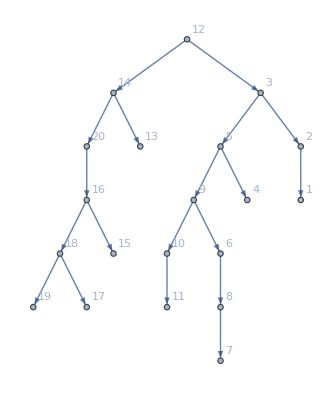
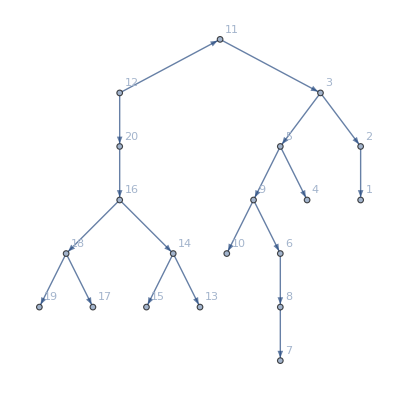
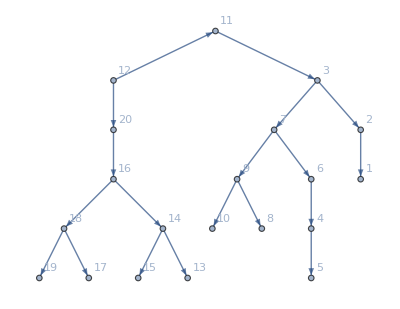
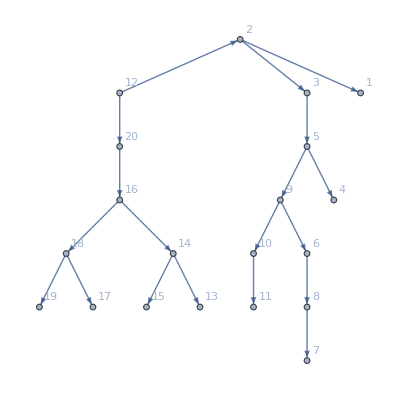
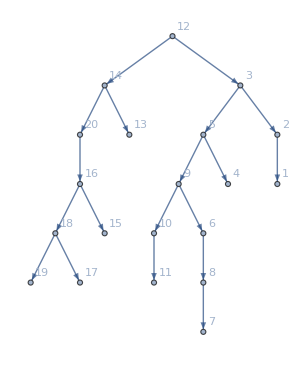

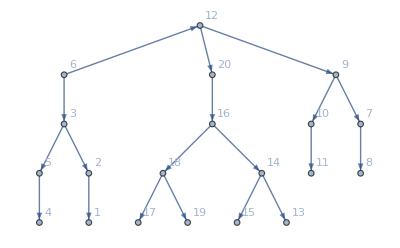
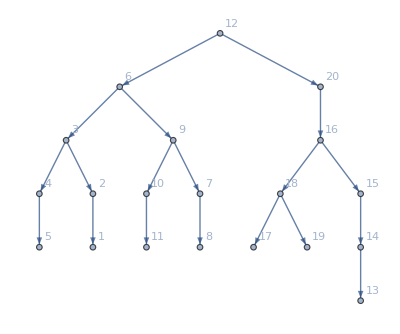
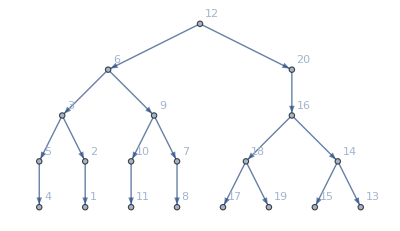

0.811837

10.015

Set::write: Tag Inherited in Inherited[State] is Protected.